```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\genobayes\\scripts"]
```

C:\Users\pglpm\repositories\genobayes\scripts

```mathematica
data=T[Import["allcondfreqs_1gene_thetamax_sA.csv"][[2;;,2;;]]];
```

```mathematica
Dimensions[data]
```

{188,6}

```mathematica
data[[1;;3,;;]]
```

{{0.270461,0.00581621,0.260939,0.280073,931.488,363.264},{0.290756,0.00860072,0.276694,0.304988,931.488,363.264},{0.275504,0.0000574049,0.27541,0.275599,4.38816×10^7,1.66869×10^7}}

```mathematica
geneseq=Import["allcondfreqs_1gene_thetamax_sA.csv"][[1,2;;]];
symptomnames={"A","B","C"};allelenames={"A","B"};
```

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
Do[
data=T[Import["allcondfreqs_1gene_thetamax_v2_s"<>sym<>".csv"][[2;;,2;;]]];
min=Min[data[[;;,1]]-data[[;;,2]]];
max=Max[data[[;;,1]]+data[[;;,2]]];plot=ErrorListPlot[data[[;;,{1,2}]],Joined->False,PlotRange->{min,max},Joined->False,AspectRatio->1/6,Frame->Auto,Axes->None,FrameLabel->{Style[gene,41],Style[freq[symptom|"gene allele"],41]},
FrameStyle->Directive[Large],
FrameTicks->{Auto,{T@{Range[94*2],Style[#,15]&/@(Rotate[#,Pi/2]&/@(geneseq))},None}},
PlotStyle->PointSize[Scaled[0.005]],GridLines->Auto,ImageSize->a4longside*{6,1},Epilog->Text[Style["symptom "<>sym,42],Sequence@@labelposition[{0.5,0.9}]]];
Export["testcf_maxtheta_v2_s"<>sym<>".pdf",plot];
,{sym,symptomnames}]
```

```mathematica
Export["testcf_A_tmax.pdf",%]
```

testcf_A_tmax.pdf

```mathematica
tdata=data[[;;,;;5]]
```

{{3323,1045,1958,2410,2708},{1214,447,740,921,1060}}

```mathematica
tdata+{t0,t1}
```

{{3323+t0,1045+t0,1958+t0,2410+t0,2708+t0},{1214+t1,447+t1,740+t1,921+t1,1060+t1}}

```mathematica
LogGamma[tdata]//N
```

{{23618.8,6217.05,12880.1,16354.6,18692.9},{7404.8,2278.71,4146.54,5362.75,6321.42}}

```mathematica
Length@T@tdata
```

5

```mathematica
logprob[t_,g_]:=Block[{r2=data[[;;,{g,g+1}]]+t},
Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])]
```

```mathematica
logprob2[x_,y_]=Block[{t={x,y},r2=data+{x,y}},
Simplify[Total@Flatten@LogGamma[r2]-
Total@LogGamma[Total@r2]+
(Length@T@r2)*(LogGamma[Total@t]-Total@LogGamma[t])]];
```

```mathematica
logprob[{10,20},1]//N
```

-3569.25

```mathematica
xy=FindMaximum[{logprob[{x,y},1],x>0,y>0},{{x,1},{y,1}}]
```

{-3548.32,{x→925.595,y→361.104}}

```mathematica
Total@Flatten@data[[;;,{1,2}]]
```

6029

```mathematica
bd[x_,a_,b_]=PDF[BetaDistribution[a,b],x]
```

Piecewise[{{((1-x)^(-1+b) x^(-1+a))/Beta[a,b], 0<x<1}, {0, True}}]

```mathematica
{a0,b0}=data[[;;,2]]
```

{1045,447}

```mathematica
{am,bm}=data[[;;,2]]+({x,y}/.xy[[2]])
```

{1970.59,808.104}

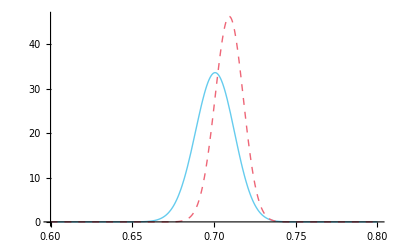

```mathematica
Plot[{bd[x,a0,b0],bd[x,am,bm]},{x,0.6,0.8},PlotRange->All]
```